```mathematica
m:=10^(-10)
omega:=2*Pi*10
I1 :=10^(-7)
mu0:=4*Pi*10^(-7)
A:=mu0*m*m'/(4*Pi*a^3)
```

```mathematica
alpha[omega_]:=Values[Solve[Cos[x]+omega^2 *Sin[x]*Cos[x]-omega*Sin[x]==0,x,Assumptions->{0<x<Pi}]]
Values[Solve[0==Sin[x]*(Cos[x]-1)-Sin[x]*Sin[y] &&
0==-Cos[y]/Sin[x]-2*Cos[x]/Sin[x],{x,y},Assumptions->{{0<x<Pi},{0<y<2*Pi}}]]
```

$Aborted

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

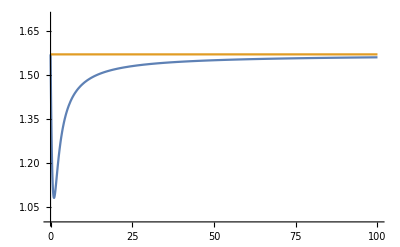

```mathematica
Plot[{alpha[omega],Pi/2,Pi/4},{omega,0,100}, PlotRange->{1,1.7}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

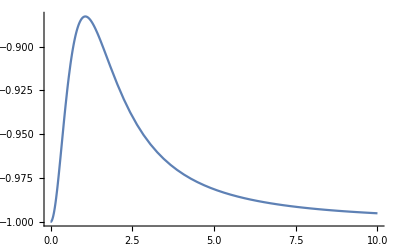

```mathematica
Plot[-Sin[alpha[omega]],{omega, 0, 10}]
```

```mathematica
Plot[-D[Sin[alpha[omega]],omega],{omega,0,10}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::ivar: 0.000204286 is not a valid variable.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::ivar: 0.204286 is not a valid variable.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

General::ivar: 0.408368 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

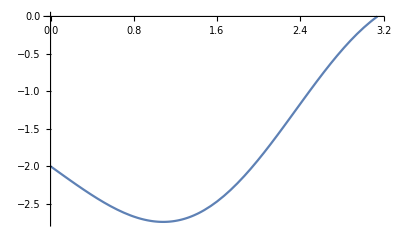

```mathematica
Plot[-Sin[x]-1-Cos[x]-Sin[x]*Sin[x]/2,{x,0,Pi}]
```

```mathematica
DynamicModule[{a},Column[{Dynamic@Plot[-Cos[a]*Sin[x]-1-Cos[x]-Sin[x]*Sin[x]/2,{x,0,Pi}],Slider[Dynamic@a,{0,10}]}]]
```

```mathematica
DSolve[{
theta''[t]==Cos[theta[t]]+Sin[theta[t]]*Cos[theta[t]]-Sin[theta[t]],
theta[0]==0,
theta'[0]==0
},theta[t],t]
```

```mathematica
FindMinValue[alpha[omega],{omega ,0,2}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Values::invrl: The argument Solve[Cos[x]-omega Sin[x]+omega^2 Cos[x] Sin[x]==0,x,Assumptions→{0<x<π}] is not a valid Association or a list of rules.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

FindMinValue::nrnum: The function value {{1.5708}} is not a real number at {omega} = {0.}.

FindMinValue[alpha[omega],{omega,0,2}]